# Geographic Distortions

## Jovana Andrejevic, Nina Andrejevic, and George Varnavides

## Following along

```mathematica
URLShorten["https://raw.githubusercontent.com/gvarnavi/generative-art-iap/master/01.22-Friday/03X_geographic-distortions.nb"]
```

https://wolfr.am/SKi2EVGZ

```mathematica
NotebookOpen["https://wolfr.am/SKi2EVGZ"]
```

## Map Distortions

Add Introduction

## Transportation Maps

A curious example where maps are deliberately geographically distorted is transportation maps

Perhaps the most popular example is the introduction of the 1931 London Underground Tube map by Harry Beck

```mathematica
SetDirectory[NotebookDirectory[]];
Import["maps/london-underground-1933.png",ImageSize->Large]
```

-Graphics-

The map has changed a bit through the decades, adding more stops and thus more distortion

```mathematica
Import["maps/london-underground-2016.png",ImageSize->Large]
```

-Graphics-

Comparing this with a geographically-accurate map of the London underground, the distortion becomes apparent

```mathematica
Import["http://www.balstone.co.uk/images/tube.png",ImageSize->Large]
```

-Graphics-

How can we use the ideas of distorted map grids we’ve talked about, to visualize this distortion?

## Distortion Grids

In order to co-locate the two maps, we need a set of reference points in both maps.

Fortunately, we have these handy by design: we can use the station names!

Fortunately, we have these handy by design: we can use the station names!

I went ahead and computed some linked reference points for old London Underground maps

How? Tediously.. Manually right-clicking to get the coordinates for the same tube station on both maps

Toyed with the idea of using image processing for this, was short on time to implement :)

```mathematica
linkedPointsFiles=FileNames["linked_points*","data"];
years=ToExpression[StringSplit[#,{"_","."}][[-2]]]&/@linkedPointsFiles
linkedPoints=Import[#,"Data"]&/@AssociationThread[years->linkedPointsFiles];
```

{1933,1938,1940,1944,1945,1946,1948}

```mathematica
linkedPoints[1933]//TableView
```

Rickmans Worth0.0287480.281348486.7860181349.932827Croxley0.0463610.278293558.4796351383.219149Watford0.0524720.284942619.9313071419.706079Moor Park0.0480690.261668583.4443771321.767477Northwood0.0556170.253581609.049241250.07386Pinner0.0628960.245853712.1088151187.341945North Marrow0.0701750.238035753.0765961163.017325Harrow on the hill0.0843730.232104804.2863221138.052584West Harrow0.0708040.225903763.3185411132.931611Rayners Lane0.0589420.220601729.3920971118.848936Eastcote0.0499560.219793676.2620061122.049544Ruisup Manor0.0418680.220512647.4565351110.527356Ruislip0.0326120.219793623.1319151099.005167Ickenham0.0239860.221141575.7629181068.279331Hillingdon0.0153590.220152552.0784191034.993009Uxbridge0.0069120.220242495.747721013.228875Northwick Park0.1036970.232256842.4594981139.586208South Harrow0.0708750.21325778.0072571081.255129Sudbury Hill0.0708080.204354809.3332071061.091299Sudbury Town0.0704030.195592853.261551042.727812Alperton0.0702690.186898896.1096881007.801178Park Royal0.0702690.178272937.157485957.391603North Ealing0.0704030.16978940.3981927.865995Ealing Broadway0.0473540.16277900.430509915.983739West Acton0.0817260.158322950.480015933.267021North Acton0.0974970.158457990.087538949.830167East Acton0.1129980.1584571021.413488924.62538Watford Junction0.0726270.283949669.6266721442.043655Watford Street0.07930.277075669.2666031402.076064Bushey0.0852980.270874691.5908431370.750114Carpenders Park0.0913640.264741695.5515961313.859309Hatch End0.0973620.258878733.3587771256.248366Headstone Lane0.1037650.252408769.7256841223.842211Harrow & Wealdstone0.1097630.246072810.773481191.075988Kenton0.1160980.240007857.2223021147.507713North Wembley0.1297120.226123888.5482521079.454787Wembley Central0.1344970.22154906.5516721045.24829Stonebridge Park0.1400240.216081951.560221023.284119Harlesden0.1446740.210891990.807675999.159536Willesden Junction0.150470.2053651029.334992984.036664Kensal Green0.1555250.1997711074.343541981.156117Queens Park0.1607140.1945821111.790653992.678305Kilburn Park0.166510.1892571135.195099999.159536Maida Vale0.1717670.1835291160.039818973.234612Warwick Avenue0.1773610.1779351166.881117957.751672Paddington0.1891560.1660731176.963032934.707295Edgware Road0.2090380.1736211192.806041944.069073Marylebone0.2204950.1734191206.848708949.470099Baker Street0.2396350.166411231.333359954.511056Regents Park0.2396350.1565031249.336778944.069073Oxford Circus0.2395010.145181255.457941927.145859Bond Street0.22710.1460561241.415274923.185106Marble Arch0.2143620.1453821224.852128920.664628Lancaster Gate0.2011520.145451193.166109915.263602Queensway0.1873360.1453821165.800912909.502508Notting Hill Gate0.1723070.1453151138.435714902.661208Holland Park0.1572770.1455171113.590995894.019567Shephers Bush0.1340930.1463261084.425456886.818199White City0.1336880.1538741073.623404909.142439Tottenham Court Road0.2591130.1451131278.502318930.746543Holborn0.283510.1447081307.667857932.546884Chancery Lane0.2974620.1452471326.031345931.466679St Pauls0.311480.145451361.678116926.065653Bank0.324420.1448431378.961398916.343807Liverpool0.3427520.1494261398.405091935.7875Piccadilly0.242870.1292071273.101292902.30114Trafalgar Square0.2552040.1164021297.225874895.819909Charing Cross0.2785230.1143131304.067173890.418883Waterloo0.2942940.1049441324.591071872.415464Lambeth North0.3067620.0980031328.551824864.493959Elephant & Castle0.3166020.0974631359.517705846.850608Preston Road0.1391560.232367892.2719221125.281269Wembley Park0.1597640.232367937.2804711089.634498Stanmore0.1379580.252496880.3896661289.112386Canons Park0.1449070.245307896.5927431254.185752Kingsbury0.1522160.238597937.640541162.728381Neasden0.169350.2323671001.0125761065.509916Dollis Hill0.1761790.2290121031.6183891055.78807Willesden Green0.182290.2231411069.7856381046.426292Kilburn0.188640.2165511107.5928191038.144719West Hampstead0.194870.210441137.1184271040.305129Finchley Road0.2012210.203971158.722531040.665198Swiss Cottage0.2070920.1980991181.4068391024.46212St Johns Wood0.2201520.1851591186.807865996.016717Edgware0.2085290.252256944.1217711271.829103Burnt Oak0.214520.246026965.3658051235.822264Colindale0.2205110.239915997.771961208.457067Hendon Central0.227460.2326061056.8231761168.489476Brent Cross0.2336910.2268551085.9887161147.245441Golders Green0.2388430.2206251132.077471130.682295Hampstead0.2450730.2141551178.1662231080.27272Belsize Park0.2513040.2078051206.9716951055.067933Chalk Farm0.2575340.2019341219.214021042.105471Camden Town0.2646030.1931871253.0604481020.141299Kentish Town0.2641240.2094821260.6218841047.146429Tufnell Park0.2641240.2232611263.86251086.753951Highgate0.2644830.237041243.3386021148.685714Cockfosters0.3067780.2842471226.4153881425.218237Oakwood0.3061790.2752611266.022911409.375228Southgate0.3068980.2669931268.9034571353.924696Arnos Grove0.3066580.2581271255.2208591300.994643Bounds Green0.3061790.2491411284.3863981268.948556Wood Green0.3066580.2407541323.2737841233.661854Turnpike Lane0.3066580.2314081340.5570671205.216451Manor House0.305820.2226621352.4393241130.322226Finsbury Park0.3035430.2119981334.0758361113.759081Arsenal0.2958750.2033711339.4768621087.834157Holloway Road0.2867690.1945051317.512691064.069643Caledonian Road0.2841330.1826431305.9905021052.547454Kings Cross St Pancras0.2830550.1724591302.389818981.253913Drayton Park0.3172020.2032521336.2362461064.069643Highbury & Islington0.3264280.1942651343.4376141048.946771Essex Road0.3293040.1828831356.7601441025.182257Old Street0.3289440.1730581381.244795970.451862Angel0.3108520.1726991337.67652992.055965Hounslow West0.0435010.103409736.077812751.466565Hounslow Central0.0479980.108079768.083891746.985714Hounslow East0.0531860.112922789.207903756.587538Osterley0.0583750.118283800.730091785.393009Boston Manor0.0635630.12278851.939818835.322492Northfields0.069270.129525877.544681844.924316South Ealing0.0742860.134713889.066869851.325532Ealing Common0.0699620.14976937.075988891.01307Acton Town0.0834520.134886946.677812868.608815South Acton0.0984990.13748978.043769875.650152Chiswick Park0.0922730.127449967.161702846.204559Turhnam Green0.0993640.1158621010.049848846.204559Gunnersbury0.0924460.108944958.840122821.879939Kew Gardens0.0805120.096318944.757447773.230699Richmond0.0704810.086287903.789666729.06231Stamford Brook0.1088760.1091171023.492401843.644073Ravescourt Park0.1199450.1037551044.616413847.484802Hammersmith0.1303220.1034091074.702128836.602736Goldhawk Road0.1301490.1265851068.300912870.529179Latimer Road0.1429470.1699951088.784802914.057447Ladbroke Grove0.1529780.1693031102.547416923.979331Westbourne Park0.1621440.1701681115.509878935.981611Royal Oak0.1714840.1693031156.317629949.424164Bayswater0.1811690.1530461152.4769921.578875High Street Kensington0.1761530.1234711145.275532870.209119Kensington Olympia0.1503840.1238171106.868237858.68693Barons Court0.1436390.1023721103.507599825.080547West Kensington0.1559180.102891118.870517824.600456Earls Court0.1761530.1037551142.394985832.762006West Brompton0.1763080.0945811139.863561818.776689Fulham Broadway0.1764710.0855321137.301082796.034689Parsons Green0.1763750.0760921125.129308774.894239Putney Bridge0.1764710.0673251112.316914748.628831East Putney0.1765680.0528761104.309167710.191648Southfields0.1762790.0439171118.402801665.027958Wimbledon Park0.1765680.035441137.621392620.184579Wimbledon0.1761820.0251321114.559083582.388016Gloucester0.1931370.1031611166.449279838.6359South Kensington0.2066230.1032571178.300744838.6359Sloane Square0.2257930.1029681228.909701837.99528Knightsbridge0.2289720.1161661217.378546869.065336Hyde Park Corner0.2337890.1201151231.79249877.713702Green Park0.2379310.124451251.97201891.487026Victoria0.242170.1031611257.737588848.565505Morden0.2355230.0172331146.269758514.802636South Wimbledon0.2412060.0235911155.879054551.63827Colliers Wood0.246890.0290821187.58973569.255312Tooting Broadway0.2528620.0349581205.527081594.55979Tooting Bec0.2587390.0407381225.386292625.309536Balham0.2645180.0465181242.362715655.738973Clapham South0.2708760.0526831250.050151692.254296Clapham Common0.2762710.0592341264.464095720.761873Clapham North0.2827250.0646281287.846714733.894577Stockwell0.2887940.0702151306.104376765.605253Oval0.2945740.0758031325.002657799.878407Kennington0.3023770.0837021343.900939822.620407St James Park0.2583530.1027751281.120207867.784097Westminster0.2721290.109231297.77632878.034012Leicester Square0.2647110.1293631289.448263915.189955Warren Street0.2591240.1610561271.030447948.261948Goodge Steet0.2594130.1539281274.633933942.49637Great Portland Street0.2499720.1692441257.096968953.066596Euston0.2596060.1730011274.3937972.044954Euston Square0.2684680.1691481279.919045961.234497Mornington Crescent0.2587390.1809971265.505102996.548658Covent Garden0.2779090.1354321301.53996923.277779Russell Square0.2836880.1552761305.383679953.787293Temple0.2876380.1230051327.244826906.701744Blackfriars0.2942850.1292671351.508298905.981047Mansion House0.3081570.1286891368.084333905.500582Cannon Street0.3202940.129171380.336185903.338491Farringdon0.3006430.1594181339.496678948.742413Aldersgate0.3154780.1592261360.637129940.574511Moorgate0.3294460.1591291382.017812938.652652Aldgate0.3516990.1369731413.728487929.523821Monument0.3331070.1293631392.107572901.656864Tower Hill0.3442810.1286891419.494065909.584533Aldgate East0.3753960.1284961435.829867940.814744Borough0.3227990.1028721371.928051868.985259London Bridge0.3241480.1098081383.699438881.237111Whitechapel0.3935070.1292671444.238001944.418229Stepney Green0.4021760.1287851472.345191954.748222Mile End0.4082450.1287851506.45819960.033335Bow Road0.4143140.129171528.799803966.039145Shadwell0.3932180.1170331449.042649917.992666Wapping0.3933140.1109641452.886367886.041758Rotherhithe0.3931210.0980551460.333571874.750836Surrey Quays0.3935070.0909271477.149839841.358534New Cross Gate0.393410.0757061489.641923781.300436New Cross0.4058370.0757061509.581211784.183224

The first column gives the reference point’s name (tube station)

```mathematica
linkedPoints[1933][[All,1]]//Short
```

{Rickmans Worth,Croxley,Watford,Moor Park,«198»,Surrey Quays,New Cross Gate,New Cross}

The second and third columns give the location of the station in the distorted map

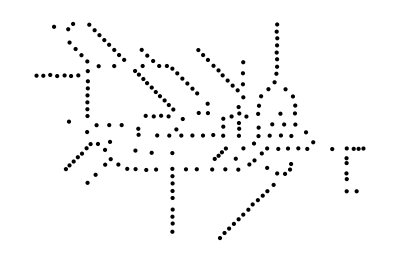

```mathematica
linkedPoints[1933][[All,2;;3]]//Point//Graphics
```

The fourth and fifth columns give the geographically-accurate location of the station

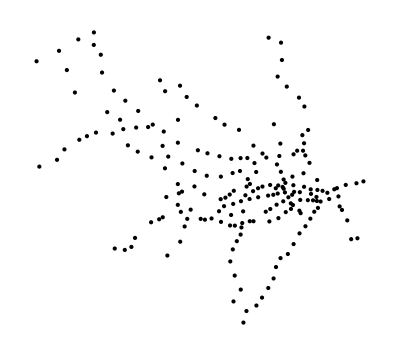

```mathematica
linkedPoints[1933][[All,4;;5]]//Point//Graphics
```

### Global Transformation

The first thing to note is that these may have different global coordinates systems

In-fact ours do, since the map images had different image dimensions (So I used relative coordinates for the distorted maps)

As such, we find the best-fit Affine transformation to transform our geographically accurate points to the distorted map’s coordinates system

```mathematica
undergroundMapPoints["old"][year_]:=linkedPoints[year][[All,2;;3]];
geographicallyAccuratePoints["new"][year_]:=linkedPoints[year][[All,4;;5]];
```

```mathematica
globalTransformation[year_]:=Block[{error,tf},
{error,tf}=FindGeometricTransform[undergroundMapPoints["old"][year],geographicallyAccuratePoints["new"][year],TransformationClass->"Affine"];
tf]
```

```mathematica
globalTransformation[1933]
```

TransformationFunction[(0.000434306 | 0.000119486 | -0.397785
-0.0000311443 | 0.000325736 | -0.118831
0. | 0. | 1.)]

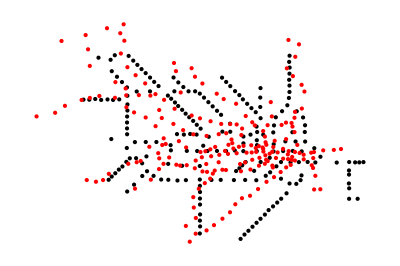

```mathematica
{undergroundMapPoints["old"][1933]//Point,Red,globalTransformation[1933][geographicallyAccuratePoints["new"][1933]]//Point}//Graphics
```

### Displacement Vectors

One simple way of visualizing the distortions, is to add displacement vectors from our reference points to where they would lie on the globally-transformed geographically accurate locations

```mathematica
displacementVectors[year_]:=With[{tf=globalTransformation[year]},
tf[geographicallyAccuratePoints["new"][year]]-undergroundMapPoints["old"][year]]
```

```mathematica
displacementVectorsGraphicsPrimitive[year_]:=With[{vecs=displacementVectors[year],controlPoints=undergroundMapPoints["old"][year]},
Arrow/@Thread[{controlPoints,controlPoints+vecs}]]
```

```mathematica
displacementVectorsRange[year_]:=MinMax/@Transpose[Flatten[displacementVectorsGraphicsPrimitive[year][[All,1]],1]]
```

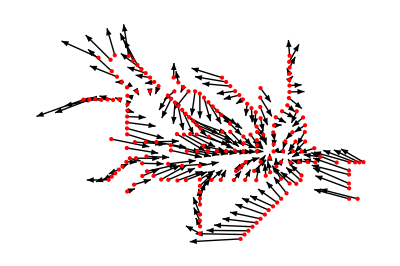

```mathematica
{Arrowheads[Medium],displacementVectorsGraphicsPrimitive[1933],Red,Point[undergroundMapPoints["old"][1933]]}//Graphics
```

### Distortion Grids

```mathematica
distanceMatrix[year_]:=DistanceMatrix[undergroundMapPoints["old"][year]]
```

```mathematica
multiquadraticInterpolationFit[year_]:=Block[
{m=ArrayFlatten[{{distanceMatrix[year],0},{0,distanceMatrix[year]}}],
b=Flatten[Transpose[displacementVectors[year]]]},
LinearSolve[m,b]
]
```

```mathematica
undistortedGrid[year_,delta_:0.005]:=Block[{minX,maxX,minY,maxY},
{{minX,maxX},{minY,maxY}}=displacementVectorsRange[year];

minX=Floor[minX,delta];
minY=Floor[minY,delta];
maxX=Ceiling[maxX,delta];
maxY=Ceiling[maxY,delta];

Tuples[{Range[minX,maxX,delta],Range[minY,maxY,delta]}
]]
```

```mathematica
Clear[pointsToGridsGraphicsPrimitive]
thread[first_,rest___]:=Thread[{first,{rest}}]
pointsToGridsGraphicsPrimitive[year_,delta_:0.005]:=pointsToGridsGraphicsPrimitive[year]=Block[{nf=Nearest[undistortedGrid[year,delta]->Automatic]},
Line/@DeleteDuplicates[Join@@thread@@@(nf[#,{All,1.05delta}]&/@undistortedGrid[year,delta])]]
```

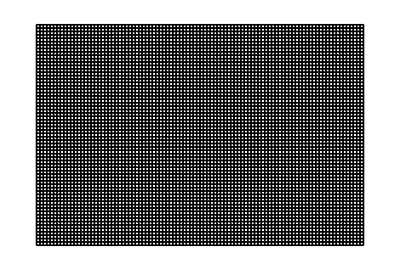

```mathematica
undistortedGridGraphicsPrimitive[year_,delta_:0.005]:=GraphicsComplex[undistortedGrid[year,delta],pointsToGridsGraphicsPrimitive[year,delta]]
undistortedGridGraphicsPrimitive[1933]//Graphics
```

```mathematica
distortedGridDisplacements[year_,delta_:0.005]:=Block[{horizontalFit,verticalFit,dm,l,horizontalDisplacements,verticalDisplacements},
l=Length[undergroundMapPoints["old"][year]];
{horizontalFit,verticalFit}=Partition[multiquadraticInterpolationFit[year],l];
dm=DistanceMatrix[undistortedGrid[year,delta],undergroundMapPoints["old"][year]];
horizontalDisplacements=dm.horizontalFit;
verticalDisplacements=dm.verticalFit;
Thread[{horizontalDisplacements,verticalDisplacements}]]
```

```mathematica
distortedGrid[year_,delta_:0.005]:=undistortedGrid[year,delta]+distortedGridDisplacements[year,delta]
distortedGridGraphicsPrimitive[year_,delta_:0.005]:=GraphicsComplex[distortedGrid[year,delta],pointsToGridsGraphicsPrimitive[year,delta]]
```

```mathematica
Clear[visualizeDistortedGrids]
visualizeDistortedGrids[year_]:=visualizeDistortedGrids[year]=Graphics[{
{Opacity[0.5],Thin,Gray,undistortedGridGraphicsPrimitive[year]},
{Black,Thin,distortedGridGraphicsPrimitive[year]},
{Blue,Arrowheads[Medium],displacementVectorsGraphicsPrimitive[year]},
{Red,PointSize[Large],Point[undergroundMapPoints["old"][year]]}},ImageSize->750]
```

```mathematica
Manipulate[visualizeDistortedGrids[year],{year,years}]
```

### Superimposing

```mathematica
distortedMap[1945]=Import["maps/london-underground-1945.png"];
```

So turns out the way I took the rescaled map coordinates this morning wasn’t very intelligent

Or at-least I’ve forgotten what I was thinking, and can’t reproduce.. (Note to self: comment more)

In any case, here’s a semi-manual way for one map (1945)

I’ll clean up the code and update again once I remember what I had in mind..

```mathematica
coords={{1077.6833976833975,232.69771170359445},{925.7142857142856,743.276862282745},{263.1660231660232,185.4390244449072},{128.80308880308883,746.9834259893088}};
mapCoordsAsc=AssociationThread[{"New Cross","Cockfosters","Richmond","Chesham"},coords]
scaledCoordsAsc=Association[Table[station->Select[linkedPoints[1945],#[[1]]==station&][[1,2;;3]],{station,Keys[mapCoordsAsc]}]]
```

<|New Cross→{1077.68,232.698},Cockfosters→{925.714,743.277},Richmond→{263.166,185.439},Chesham→{128.803,746.983}|>

<|New Cross→{0.379918,0.082018},Cockfosters→{0.326778,0.26196},Richmond→{0.092605,0.065957},Chesham→{0.045536,0.26333}|>

```mathematica
tf=With[{
rescaleX=Rescale[x,{0.045536,0.379918},{128.8,1077.68}],
rescaleY=Rescale[y,{0.065957,0.26196},{185.4,743.28}]
},
AffineTransform[{
{{Coefficient[rescaleX,x, 1],0},{0,Coefficient[rescaleY,y, 1]}}
,{Coefficient[rescaleX,x, 0],Coefficient[rescaleY,y, 0]}}]];
```

```mathematica
ImageCompose[distortedMap[1945],With[{dims=distortedMap[1945]//ImageDimensions},
Rasterize[Graphics[GeometricTransformation[First[visualizeDistortedGrids[1945]],tf],PlotRange->Thread[{1,dims}],PlotRangePadding->None,PlotRangeClipping->True,Background->None],
RasterSize->dims,ImageSize->dims,Background->None]]]
```

-Graphics-